```mathematica
(*Основано на ReadTormagn и FindingOmegaSA*)
```

```mathematica
FileNames["ponom(*"]
```

{ponom(kappa=0.25,k=1.00).snp}

#### Общий анализ

```mathematica
nom=12;
k=0.35-0.02nom
k1=1.15;
kstr=ToString[k];While[StringLength[kstr]<4,kstr=kstr<>"0"];
```

0.11

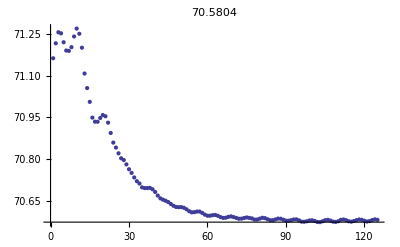

```mathematica
ListPlot[ToExpression/@cs[[nom,2]],PlotLabel->cs[[nom,2,-1]]]
```

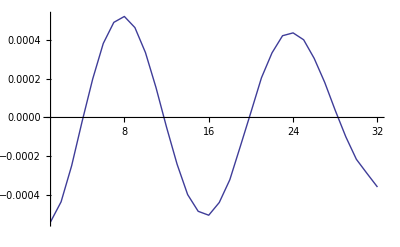

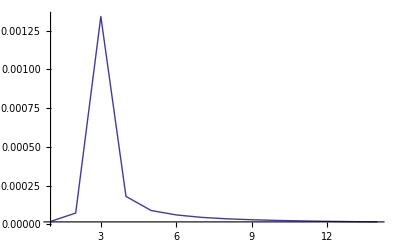

8.72675

```mathematica
out=.;ReadBinarySnapFile["ponom("<>ToString[k]<>").snp",6,out,PrintInfo->None];
{coor,bounds}=ReadAuxFiles[{"coord"},ShiftVector->{4,0,0}];
{Bx,By,Bz}=rotc[Sequence@@Take[out,-3],3];
PrintRange[WithoutFict@Bx⟦10,All,25⟧]
PrintRange[Take[Abs@Fourier@WithoutFict@Bx⟦10,All,25⟧,14]]
-10Log[10,HarmClearance[WithoutFict@Bx⟦10,All,25⟧]]
```

```mathematica
grB=DrawSection[Bx,By,Bz]
```

GraphicsArray::obs: GraphicsArray is obsolete. Switching to GraphicsGrid.

-Graphics-

```mathematica
Export["B(kappa=0.25,chi=0.3,k="<>ToString[k]<>").png",grB,ImageResolution->300,ImageSize->640];
```

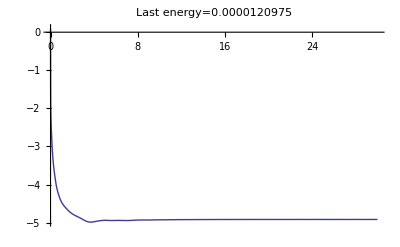

```mathematica
len=Transpose[Select[Import["energy(kappa=0.25,k="<>kstr<>").dat","Table"],(0<First[#])&]];
ltm=First[len];(*PrintRange[dif[ltm],All,PlotLabel->"Time step"]*)
{mp,mdp,mvx,mdvx,mvy,mdvy,mvz,mdvz,mAx,mdAx,mAy,mdAy,mAz,mdAz,mBx,mBy,mBz,mqp,mqvx,mqvy,mqvz,mqAx,mqAy,mqAz,mqBx,mqBy,mqBz}=Transpose[{ltm,#}]&/@Drop[len,2];
(*PrintRange[{#⟦1⟧/3,#⟦2⟧}&/@(mqvx+mqvy+mqvz)]*)
(*PrintRange[{#⟦1⟧/3,Log[10,#⟦2⟧]}&/@(mqAx+mqAy+mqAz),All,PlotLabel->"Last energy="<>ToString[Last[Last[mqAx+mqAy+mqAz]]]]*)
PrintRange[{#⟦1⟧/3,Log[10,#⟦2⟧]}&/@(mqBx+mqBy+mqBz),All,
PlotLabel->"Last energy="<>ToString[Last[Last[mqBx+mqBy+mqBz]]]]
```

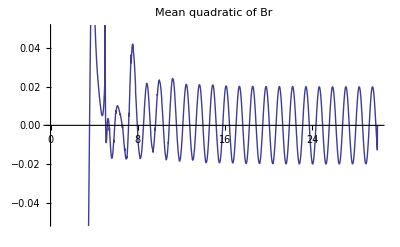
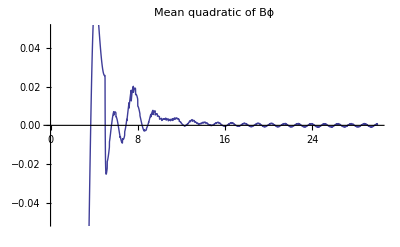
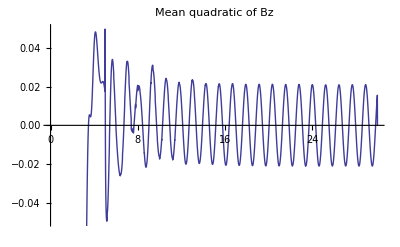

```mathematica
grs=MapThread[PrintRange[#1,0All+0.05{-1,1},PlotLabel->#2]&,{dif[Map[Function[l,{l⟦1⟧,Log[l⟦2⟧]/2}],#]]&/@{mqBx,mqBy,mqBz},{"Mean quadratic of Br","Mean quadratic of Bϕ","Mean quadratic of Bz"}}]
```

```mathematica
test=Select[mBz,15<First[#]-0<30&];
```

```mathematica
Table[interpol[#,-⌊Length[#]/part⌋,-1],{part,4,1,-1}]&[test]
```

{{-0.995756,0.136521,0.876131},{-0.0000116226,2.57204,8.38132×10^-10},{0.712494,0.133495,0.924951},{0.000113331,2.57225,5.94933×10^-7}}

```mathematica
cwd=ContinuousWaveletTransform[Last/@test,MorletWavelet[]];
WaveletScalogram[cwd];
```

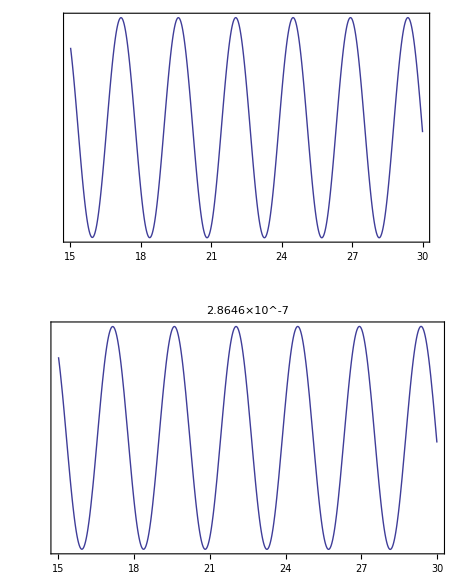

```mathematica
GraphicsGrid[{{ListLinePlot[test,Frame->True,Axes->True,FrameTicks->{Automatic,None},ImageSize->400]},{Plot[func,{t,test⟦1,1⟧,test⟦-1,1⟧},Frame->True,FrameTicks->{Automatic,None},ImageSize->430,PlotLabel->1-Correlation[Last/@test,func/.t->(First/@test)]]}}]
```

```mathematica
interpol[#,-⌊Length[#]/4⌋,-1]&[test]
```

{-0.995756,0.136521,0.876131}

#### Нахождение частоты высокочастотной компоненты

```mathematica
m2=Max[Last/@test]
```

3.29614×10^-7

```mathematica
Position[test,%]
```

{{9,2}}

```mathematica
m1=func/.t->test[[9,1]]
```

0.216829

```mathematica
test={First[#],Last[#]-m2/m1(func/.t->First[#])}&/@test;
```

Вычитание среднего

```mathematica
test=Select[test,14<First[#]<14.9&];
```

```mathematica
mean=Mean[Last/@test]
```

-2.4466×10^-6

```mathematica
test={First[#],Last[#]-mean}&/@test;
```